The Legendre Polynomials are well-known to be orthogonal and complete over the closed interval [-1, 1]. For example, here are the inner products between the first 6 Legendre Polynomials.

```mathematica
MatrixForm[Table[∫_-1^1 LegendreP[i,x]LegendreP[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0 | 0
0 | 0 | 0 | 2/7 | 0 | 0
0 | 0 | 0 | 0 | 2/9 | 0
0 | 0 | 0 | 0 | 0 | 2/11)

We can easily normalize to make them orthonormal.

```mathematica
Clear[LegendreP Norm]
LegendreP Norm[n_,x_]:=√((2n+1)/2)LegendreP[n,x]
```

```mathematica
MatrixForm[Table[∫_-1^1 LegendreP Norm[i,x]LegendreP Norm[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

It might be useful for it to be orthogonal and complete over some other interval, such as [-π, π].

```mathematica
Clear[LegendreP1]
LegendreP1[n_,x_]:=LegendreP[n,x/π]
```

```mathematica
MatrixForm[Table[∫_-π^π LegendreP1[i,x]LegendreP1[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(2 π | 0 | 0 | 0 | 0 | 0
0 | (2 π)/3 | 0 | 0 | 0 | 0
0 | 0 | (2 π)/5 | 0 | 0 | 0
0 | 0 | 0 | (2 π)/7 | 0 | 0
0 | 0 | 0 | 0 | (2 π)/9 | 0
0 | 0 | 0 | 0 | 0 | (2 π)/11)

Again we can normalize this

```mathematica
Clear[LegendreP1 Norm]
LegendreP1 Norm[n_,x_]:=√((2n+1)/(2π))LegendreP1[n,x]
```

```mathematica
MatrixForm[Table[∫_-π^π LegendreP1 Norm[i,x]LegendreP1 Norm[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

The Legendre polynomials satify the recurrence

```mathematica
Clear[LegendreP Re]
LegendreP Re[0, x_]:=1
LegendreP Re[1, x_]:=x
LegendreP Re[n_, x_]:=LegendreP Re[n,x]=(2n-1)/n x LegendreP Re[n-1, x]-(n-1)/n LegendreP Re[n-2, x]
```

Let’s do a quick sanity check

```mathematica
Table[LegendreP[i,x]== LegendreP Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Likewise, we can give a recursive definition for the normalized version

```mathematica
Clear[LegendreP Norm Re]
LegendreP Norm Re[0, x_]:=√(1/2)
LegendreP Norm Re[1, x_]:=√(3/2)x
LegendreP Norm Re[n_, x_]:=LegendreP Norm Re[n,x]=x (√(4 n^2-1))/n LegendreP Norm Re[n-1, x]-(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n LegendreP Norm Re[n-2, x]
```

```mathematica
Table[LegendreP Norm[i, x]== LegendreP Norm Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

For completeness, we give the recursive definitions of all the variations of the Legendre polynomials we have provided above

```mathematica
Clear[LegendreP1 Re]
LegendreP1 Re[0, x_]:=1
LegendreP1 Re[1, x_]:=x/π
LegendreP1 Re[n_, x_]:=LegendreP1 Re[n,x]=(2n-1)/(π n) x LegendreP1 Re[n-1,  x]-(n-1)/n LegendreP1 Re[n-2,  x]
```

```mathematica
Table[LegendreP1[i, x]== LegendreP1 Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Clear[LegendreP1 Norm Re]
LegendreP1 Norm Re[0, x_]:=√(1/(2π))
LegendreP1 Norm Re[1, x_]:=√(3/(2π))x/π
LegendreP1 Norm Re[n_, x_]:=LegendreP1 Norm Re[n,x]=(√(4 n^2-1))/(π n)x  LegendreP1 Norm Re[n-1, x]-(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n LegendreP1 Norm Re[n-2, x]
```

```mathematica
Table[LegendreP1 Norm[i, x]== LegendreP1 Norm Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

While I am fairly certain the definition of orthonormality does not allow even constant factors, this is still done in many places, particularly the application this notebook is intended for. For completeness, I include a “relaxed” version of orthonormality until I clarify what exactly constitutes orthonormality.

```mathematica
Clear[LegendreP Norm1]
LegendreP Norm1[n_,x_]:=√(2n+1)LegendreP[n,x]
```

```mathematica
MatrixForm[Table[1/2∫_-1^1 LegendreP Norm1[i,x]LegendreP Norm1[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Clear[LegendreP1 Norm1]
LegendreP1 Norm1[n_,x_]:=√(2n+1)LegendreP1[n,x]
```

```mathematica
MatrixForm[Table[1/(2π)∫_-π^π LegendreP1 Norm1[i,x]LegendreP1 Norm1[j,x]ⅆx,{i,0,5}, {j,0,5}]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Clear[LegendreP Norm1 Re]
LegendreP Norm1 Re[0, x_]:=1
LegendreP Norm1 Re[1, x_]:=√3 x
LegendreP Norm1 Re[n_, x_]:=LegendreP Norm1 Re[n,x]=x (√(4 n^2-1))/n LegendreP Norm1 Re[n-1, x]-(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n LegendreP Norm1 Re[n-2, x]
```

```mathematica
Table[LegendreP Norm1[i, x]== LegendreP Norm1 Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Clear[LegendreP1 Norm1 Re]
LegendreP1 Norm1 Re[0, x_]:=1
LegendreP1 Norm1 Re[1, x_]:=(√3)/π x
LegendreP1 Norm1 Re[n_, x_]:=LegendreP1 Norm1 Re[n,x]=(√(4 n^2-1))/(π n)x LegendreP1 Norm1 Re[n-1, x]-(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n LegendreP1 Norm1 Re[n-2, x]
```

```mathematica
Table[LegendreP1 Norm1[i, x]== LegendreP1 Norm1 Re[i,x],{i,0,15}]// Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

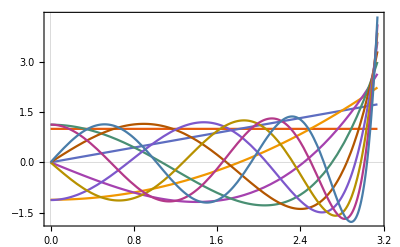

```mathematica
Plot[Evaluate[Table[LegendreP1 Norm1 Re[i,x],{i,0,9}]],{x,0,π},PlotTheme->"Scientific"]
```

To define the Chromatic derivative, we are required to express it as a Legendre polynomial of the differential operator. However, we cannot simply say

```mathematica
Clear[KD]
KD[f_,{x_, n_}] := (-ⅈ)^n LegendreP1 Norm1[n,ⅈ D[f,x]]
```

since multiplication will not correspond to function/operator composition. For the same reason, we can’t use

```mathematica
Clear[KD]
KD[n_, x_]:=(-ⅈ)^n LegendreP1 Norm1[n,ⅈ D[#,x]]&
```

Until we figure out how to compose polynomials with operators in a way that makes sense, i.e. multiplication means function composition, we will have to recursively define the Chromatic derivatives like we did the Legendre polynomials. Luckily, this isn’t that much of a nuisance.

```mathematica
Clear[KD]
KD[f_,{x_, 0}] := f
KD[f_,{x_, 1}] := (√3)/π D[f, x]
KD[f_, {x_,n_}]:=KD[f,{x,n}]=(√(4 n^2-1))/(π n) D[KD[f, {x,n-1}], x]+(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n KD[f,{x,n-2}]
```

Sanity test

```mathematica
KD[4Cos[t]-Exp[t],{t, 4}] //Simplify
```

-(3 (ⅇ^t (35+30 π^2+3 π^4)-4 (35-30 π^2+3 π^4) Cos[t]))/(8 π^4)

```mathematica
KD[ⅇ^(ⅈ ω t),{t, 4}] //Simplify
```

(3 ⅇ^(ⅈ t ω) (3 π^4-30 π^2 ω^2+35 ω^4))/(8 π^4)

```mathematica
ⅈ^4 LegendreP1 Norm1 Re[4,ω] ⅇ^(ⅈ ω t)//Simplify
```

(3 ⅇ^(ⅈ t ω) (3 π^4-30 π^2 ω^2+35 ω^4))/(8 π^4)

```mathematica
Table[KD[ⅇ^(ⅈ ω t),{t, j}]==ⅈ^j LegendreP1 Norm1 Re[j,ω] ⅇ^(ⅈ ω t),{j,0,15}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

It may be more natural to define it as an operator

```mathematica
Clear[KD Op]
KD Op[x_,0] := Identity
KD Op[x_,1] :=(√3)/π D[#,x]&
KD Op[x_,n_]:=KD Op[x,n]=(√(4 n^2-1))/(π n)D[KD Op[x,n-1]@#, x]+(√(4 n^2-1))/(√(4(n-1)^2-1)) (n-1)/n KD Op[x,n-2]@#&
```

Sanity test

```mathematica
KD Op[t,4][4Cos[t]-Exp[t]] // Simplify
```

-(3 (ⅇ^t (35+30 π^2+3 π^4)-4 (35-30 π^2+3 π^4) Cos[t]))/(8 π^4)

```mathematica
KD Op[t,4][ⅇ^(ⅈ  ω t)] // Simplify
```

(3 ⅇ^(ⅈ t ω) (3 π^4-30 π^2 ω^2+35 ω^4))/(8 π^4)

```mathematica
Table[KD Op[t,j][ⅇ^(ⅈ  ω t)]==ⅈ^j LegendreP1 Norm1 Re[j,ω] ⅇ^(ⅈ ω t),{j,0,15}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[KD Op[t,j][ⅇ^(ⅈ  ω t)]==KD[ⅇ^(ⅈ ω t),{t, j}],{j,0,15}]//Simplify
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Some examples. Here is a sinosoidal.

```mathematica
Clear[f]
f[t_]:=Cos[(π t)/5]+1/5 Cos[(9 π t)/10]+1/10 Sin[(3 π t)/10]
```

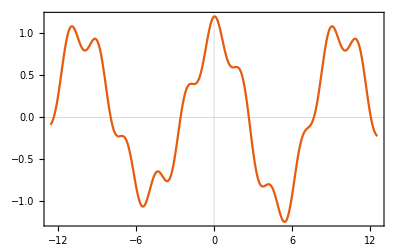

```mathematica
Plot[f[t],{t,-4 π,4 π},PlotTheme->"Scientific"]
```

Its derivative of order 3 is given by

```mathematica
D[f[t],{t,3}] // Simplify
```

(π^3 (-27 Cos[(3 π t)/10]+80 Sin[(π t)/5]+1458 Sin[(9 π t)/10]))/10000

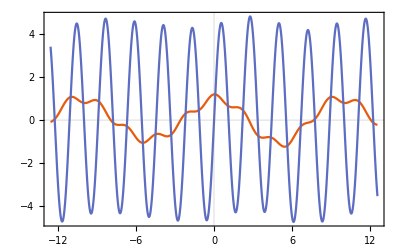

```mathematica
Plot[{f[t],Evaluate[D[f[t], {t,3}]]},{t,-4 π,4 π},PlotTheme->"Scientific"]
```

Its Chromatic derivative of order 3 is

```mathematica
KD[f[t],{t,3}]//Simplify
```

(√7 (153 Cos[(3 π t)/10]-1120 Sin[(π t)/5]+378 Sin[(9 π t)/10]))/4000

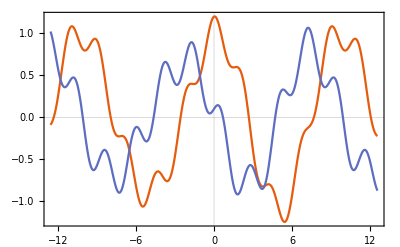

```mathematica
Plot[{f[t],Evaluate[KD[f[t],{t,3}]]},{t,-4 π,4 π},PlotTheme->"Scientific"]
```

Now let us define the chromatic expansions

```mathematica
Clear[KSeries]
KSeries[f_,{x_,n_}]:=KSeries[f,{x,n}]=∑_(i=0)^n (KD[f,{x,i}]/.t-> 0)√(2i+1)SphericalBesselJ[i,π t]
```

```mathematica
Clear[ShannonWhittaker]
ShannonWhittaker[f_,{x_,n_}]:=ShannonWhittaker[f,{x,n}]=∑_(i=-n)^n (f/.t->i)Sinc[π(t-i)]
```

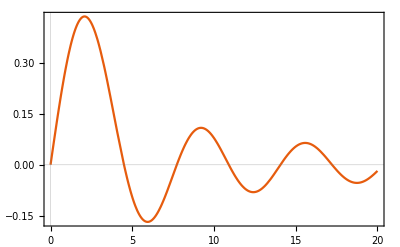

```mathematica
Plot[SphericalBesselJ[1,x],{x,0,20},PlotTheme->"Scientific"]
```

```mathematica
Clear[f]
f[t_]:=Cos[(π t)/5]+1/5 Cos[(9 π t)/10]+1/10 Sin[(3 π t)/10]
```

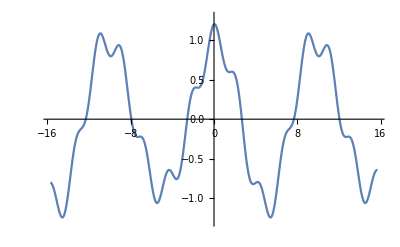

```mathematica
Plot[f[t],{t,-5π,5π},PlotRange-> {-1.3,1.3}]
```

```mathematica
Clear[g,h]
g[t_]:=Evaluate@Normal@Series[f[t],{t,0,21}]
h[t_]:=Evaluate@KSeries[f[t],{t,21}]
k[t_]:=Evaluate@ShannonWhittaker[f[t],{t,10}]
```

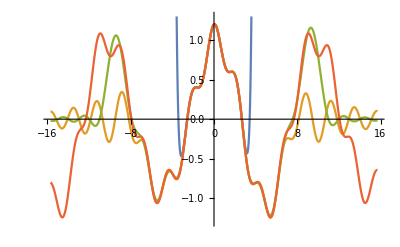

```mathematica
Plot[{g[t],h[t],k[t],f[t]},{t,-5π,5π},PlotRange-> {-1.3,1.3}]
```

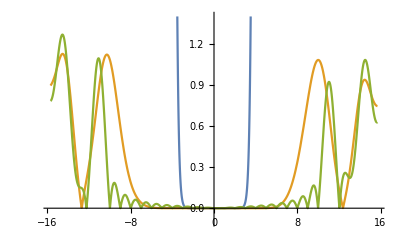

```mathematica
Plot[{Abs[f[t]-g[t]],Abs[f[t]-h[t]],Abs[f[t]-k[t]]},{t,-5π,5π},PlotRange-> {-0.1,1.4}]
```

The frequency response of the normalized higher order differential operator 1/π^n(∂_t)^n is given by (ⅈ^n(ω/π))^n. The amplitude response represents the system’s tendency to amplify or attenuate the input signal and is given by | (ⅈ^n(ω/π))^n|

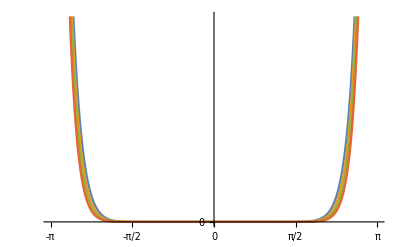

```mathematica
Plot[Evaluate@Table[Abs[(ω/π)^n],{n,15,18}],{ω,-π,π},Ticks->{Range[-Pi,Pi,Pi/2]}]
```

The frequency response of the chromatic derivative operator K^n is given by ⅈ^n P_n(ω). The amplitude response represents the system’s tendency to amplify or attenuate the input signal and is given by |P_n(ω)|

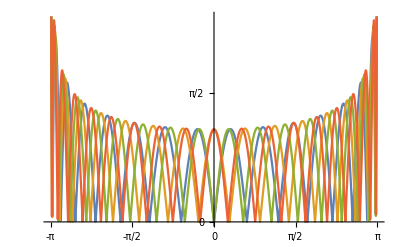

```mathematica
Plot[Evaluate@Table[Abs[LegendreP1 Norm1[n,ω]],{n,15,18}],{ω,-π,π},Ticks->{Range[-Pi,Pi,Pi/2]}]
```